### Define useful functions

```mathematica
(*==========================*)
(*delta function*)
Delta[m_, n_]:=DiscreteDelta[m-n]
(*theta function*)
Theta[m_, m0_:0]:=UnitStep[m-m0]
(*translate function*)
(*return one d index*)
Trans[m_, n_]:=m*(N0+1)+n+1
BackTrans[ii_]:= {IntegerPart[Max[(ii-1)/(N0+1),0]], Mod[ii-1, N0+1]}

(*force function*)
Kf[m_, F_,f_]:=If[m==0,0,Exp[F/(m f)]];
```

```mathematica
(*==========================*)
Clear[DecodeEntry]
(*DecodeEntry[m1_,n1_, m2_, n2_]:=
(k1off Kf[m1+1, F, f1] * (m1+1)Delta[m1+1, m2]Delta[n1-1, n2]Theta[n1-1]Theta[N0, m1+1]+
k2off Kf[m1+1, F, f2] *(m1+1)Delta[m1+1, m2]Delta[n1,n2]Theta[N0, m1+1]+
k1on*(n1+1)Delta[m1-1,m2]Delta[n1+1, n2]Theta[m1-1,1]Theta[N0, n1+1]+
k2on*(N0-m1-n1+1)Delta[m1-1, m2]Delta[n1, n2]Theta[m1-1,1]-
(k1off Kf[m1, F, f1] *m1+k2off Kf[m1, F, f2]*m1 +n1*k1on + (N0-m1-n1)*k2on)Delta[m1,m2]Delta[n1,n2])Theta[N0, m1+n1]Theta[N0, m2+n2]Theta[m2,1]Theta[m1,1];*)

DecodeEntry[m1_,n1_, m2_, n2_]:=
(k1off Kf[m1+1, F, f1] * (m1+1)Delta[m1+1, m2]Delta[n1-1, n2]Theta[n1-1]Theta[N0, m1+1]+
k2off Kf[m1+1, F, f2]*(m1+1)Delta[m1+1, m2]Delta[n1,n2]Theta[N0, m1+1]+
kon*(n1+1)Delta[m1-1,m2]Delta[n1+1, n2]Theta[m1-1,1]Theta[N0, n1+1]+
kon*(N0-m1-n1+1)Delta[m1-1, m2]Delta[n1, n2]Theta[m1-1,1]-
(k1off Kf[m1, F, f1]*m1+k2off Kf[m1, F, f2]*m1 + (N0-m1)*kon)Delta[m1,m2]Delta[n1,n2])Theta[N0, m1+n1]Theta[N0, m2+n2]Theta[m2,1]Theta[m1,1];

Clear[Entry];
Entry[ii_, jj_]:=
DecodeEntry[BackTrans[ii][[1]], BackTrans[ii][[2]], BackTrans[jj][[1]], BackTrans[jj][[2]]]
```

### Linear solver

```mathematica
N0=10;
Clear[solverN, solver]
Clear[k2off, F, koon, check, k1off, f1, f2]
solverN[k2off_, F_, kon_, check_:False]:=Module[{threshold=10^(-4), k1off=1,f1=4012/1500,f2=4012/2000},
If[Abs[F]<threshold,
PTable=Table[{i,N[Binomial[N0, i]k1off^i k2off^(N0-i)/(k1off+k2off)^N0]},{i,0,N0}],
PTable =solver[k2off, F, kon, k1off, f1, f2, check, simplify=False]];
If[Abs[Sum[PTable[[i, 2]],{i,1, N0+1}]-1]>threshold, Print["total probability not equal 1, sum=", Sum[PTable[[i, 2]],{i,1, N0+1}]]];
PTable
]


solver[k2off_, F_, kon_, k1off_, f1_, f2_, check_:False, simplify_:True]:=Module[{},

(*matrix generator*)
Clear[DecodeEntryN];
DecodeEntryN[m1_,n1_, m2_, n2_]:=
(k1off Kf[m1+1, F, f1] * (m1+1)Delta[m1+1, m2]Delta[n1-1, n2]Theta[n1-1]Theta[N0, m1+1]+
k2off Kf[m1+1, F, f2]*(m1+1)Delta[m1+1, m2]Delta[n1,n2]Theta[N0, m1+1]+
kon*(n1+1)Delta[m1-1,m2]Delta[n1+1, n2]Theta[m1-1,1]Theta[N0, n1+1]+
kon*(N0-m1-n1+1)Delta[m1-1, m2]Delta[n1, n2]Theta[m1-1,1]-
(k1off Kf[m1, F, f1]*m1+k2off Kf[m1, F, f2]*m1 + (N0-m1)*kon)Delta[m1,m2]Delta[n1,n2])Theta[N0, m1+n1]Theta[N0, m2+n2]Theta[m2,1]Theta[m1,1];

Clear[EntryN];
EntryN[ii_, jj_]:=
DecodeEntryN[BackTrans[ii][[1]], BackTrans[ii][[2]], BackTrans[jj][[1]], BackTrans[jj][[2]]];


(*matrix*)
Clear[A];
A = Table[0, {i,(N0+1)^2}, {j,(N0+1)^2}];
For[i=1, i<(N0+1)^2+1,i++,{
For[j=1, j<(N0+1)^2+1, j++, {
A[[i, j]] = EntryN[i, j]
}]
}];

(*state vector*)
Clear[x,t,i];
X = Table[x[i], {i, (N0+1)^2}];

(*vec b*)
Clear[B];
B= Table[0,{i,(N0+1)^2}];
B[[Trans[N0, 0]]]=-1;


(*linear system*)
Clear[system];
system={A.X==B};

(*solve it*)
Clear[sol];
If[ NumberQ[k2off],If[IntegerQ[k2off], sol=LinearSolve[A, B],
sol=LinearSolve[A, B, Method->"Multifrontal"]], sol=LinearSolve[A, B]];

(*load the solution*)
Clear[Q1Table,PTable];
Q1Table = Table[If[simplify, Simplify[sol[[Trans[1, i]]]], sol[[Trans[1, i]]]], {i, 0 ,N0}];
(*If[check, Print["Q1 Table=", Q1Table]];*)

PTable = Table[{i-1, k1off Kf[1,F,f1]*Q1Table[[i-1]]*Theta[i, 2]+k2off  Kf[1,F,f2]*Q1Table[[i]]*Theta[N0, i]},{i, 1, N0+1}];

If[check, Print["P Table=", PTable]];
If[check,
{Print["prob. table=", PTable];
Print["binomal tab=", Table[N[Binomial[N0, i]k1off^i k2off^(N0-i)/(k1off+k2off)^N0],{i,0,N0}]];
Print["no-rebind mean=", Sum[k1off Kf[i, F, f1]/(k2off Kf[i, F, f2]+k1off Kf[i, F, f1]),{i,1, N0}],
", calculated mean=",Sum[(i-1)*PTable[[i, 2]],{i,1, N0+1}] ];
Print["no-rebind std=", Sqrt[Sum[k1off Kf[i, F, f1] k2off Kf[i, F, f2]/(k2off Kf[i, F, f2]+k1off Kf[i, F, f1])^2,{i,1, N0}]],
", calculated std=", Sqrt[Sum[(i-1)^2*PTable[[i, 2]],{i,1, N0+1}]-Sum[(i-1)*PTable[[i, 2]],{i,1, N0+1}]^2]];
}
];
(*calculate the mean*)
Clear[nMean, nStd];
nMean = Sum[(i-1)*PTable[[i,2]],{i,1,N0+1}];
nStd = Sqrt[Sum[(i-1)^2*PTable[[i,2]],{i,1,N0+1}]-nMean^2];

(*return the mean and std*)
(*{nMean, nStd}*)
PTable
]
```

```mathematica
N0=3;
Clear[findNMean];
findNMean[k2off_, F_, kon_, check_:False]:=Module[{threshold=10^(-4),k1off=1,f1=4012/1500,f2=4012/2000},

(*delta function*)
Delta[m_, n_]:=DiscreteDelta[m-n];
(*theta function*)
Theta[m_, m0_:0]:=UnitStep[m-m0];

Clear[rm, sm, gm];
rm[m_]:=m k1off Exp[F /(m f1)];
sm[m_]:=m k2off Exp[F/(m f2)];
gm[m_]:=kon (N0-m);

Clear[fmTable];
fmTable =Table[0, {i, N0}];
fmTable[[1]] = 1/(rm[1]+sm[1]);
fmTable[[2]] = (1+kon (N0-1)/(rm[1]+sm[1]))/(rm[2]+sm[2]);
For[i=3,i<=N0, i++,
fmTable[[i]] = ((rm[i-1]+sm[i-1]+gm[i-1])fmTable[[i-1]]-gm[i-2]fmTable[[i-2]])/(rm[i]+sm[i])
];
(*Clear[diff];
diff= Abs[(rm[N0]+sm[N0])fmTable[[N0]]-gm[N0-1]fmTable[[N0-1]]-1];
If[diff>threshold, {Print["Error!! fmTable incorrect, diff=", diff];Print[fmTable]}];
Clear[diff];*)

Clear[amTable, bmTable,cmTable, dmTable];
amTable = Table[gm[m1]Theta[m1-1, 1],{m1, 1, N0-1}];
bmTable = Table[-(rm[m1]+sm[m1]+gm[m1]),{m1, 1, N0-1}];
cmTable = Table[(rm[m1+1]+sm[m1+1])Theta[N0-1, m1+1],{m1, 1, N0-1}];
dmTable = Table[-rm[i+1]fmTable[[i+1]],{i,N0-1}];

Clear[cPrime, dPrime, xOut];
cPrime[x_,{ax_,bx_,cx_}]:=cx/(bx-x ax);
dPrime[x_,{ax_,bx_,cpx_,dx_}]:=(dx-x ax)/(bx-cpx ax);
xOut[x_,{cpx_,dpx_}]:=dpx-x cpx;

Clear[cp, dp, out, triThomas];
cp=Rest[FoldList[cPrime,cmTable[[1]]/bmTable[[1]],Transpose[{amTable,bmTable,cmTable}]]];
dp=Rest[FoldList[dPrime,dmTable[[1]]/bmTable[[1]],Transpose[{amTable,bmTable,Flatten[{0,Drop[cp,-1]}],dmTable}]]];
out=Reverse[FoldList[xOut,dp[[N0-1]],Transpose[{Rest[Reverse[cp]],Rest[Reverse[dp]]}]]];
triThomas[a_,b_,c_,d_]:=Module[{cp,dp},cp=Rest[FoldList[#2[[3]]/(#2[[2]]-#1 #2[[1]])&,c[[1]]/b[[1]],Transpose[{a,b,c}]]];
dp=Rest[FoldList[(#2[[4]]-#1 #2[[1]])/(#2[[2]]-#2[[3]] #2[[1]])&,d[[1]]/b[[1]],Transpose[{a,b,Flatten[{0,Drop[cp,-1]}],d}]]];
Reverse[FoldList[(#2[[2]]-#1 #2[[1]])&,dp[[N0-1]],Transpose[{Rest[Reverse[cp]],Rest[Reverse[dp]]}]]]];

Clear[GmTable];
GmTable=triThomas[amTable,bmTable,cmTable,dmTable];
If[check, Print["no-rebind, nmean=",N[Sum[rm[i]/(rm[i]+sm[i]),{i,1, N0}]] ]];
If[check,{ 
ndis=solverN[k2off, F, kon];
Print["expected exact nmean=", N[Sum[(i-1)*ndis[[i]][[2]],{i, 1, N0+1}]]]}];
ret=(rm[1]+sm[1])GmTable[[1]]+rm[1]fmTable[[1]];
Clear[rm, sm, GmTable, fmTable, gm, amTable, bmTable,cmTable, dmTable,cp, dp, out, triThomas];
If[check, Print["calculated mean=", ret]];
ret
]
N0=5;
N[findNMean[0.1,200, 10, True],9]
```

no-rebind, nmean=0.0858027

expected exact nmean=0.0858027

calculated mean=0.0858027

0.0858027

## Calculate the variance

```mathematica
N0=3;
Clear[findNStd];
findNStd[k2off_, F_, kon_, check_:False]:=Module[{threshold=10^(-4),k1off=1,f1=4012/1500,f2=4012/2000},

(*delta function*)
Delta[m_, n_]:=DiscreteDelta[m-n];
(*theta function*)
Theta[m_, m0_:0]:=UnitStep[m-m0];

Clear[rm, sm, gm];
rm[m_]:=m k1off Exp[F /(m f1)];
sm[m_]:=m k2off Exp[F/(m f2)];
gm[m_]:=kon (N0-m);

Clear[fmTable];
fmTable =Table[0, {i, N0}];
fmTable[[1]] = 1/(rm[1]+sm[1]);
fmTable[[2]] = (1+kon (N0-1)/(rm[1]+sm[1]))/(rm[2]+sm[2]);
For[i=3,i<=N0, i++,
fmTable[[i]] = ((rm[i-1]+sm[i-1]+gm[i-1])fmTable[[i-1]]-gm[i-2]fmTable[[i-2]])/(rm[i]+sm[i])
];
(*Clear[diff];
diff= Abs[(rm[N0]+sm[N0])fmTable[[N0]]-gm[N0-1]fmTable[[N0-1]]-1];
If[diff>threshold, {Print["Error!! fmTable incorrect, diff=", diff];Print[fmTable]}];
Clear[diff];*)

Clear[amTable, bmTable,cmTable, dmTable];
amTable = Table[gm[m1]Theta[m1-1, 1],{m1, 1, N0-1}];
bmTable = Table[-(rm[m1]+sm[m1]+gm[m1]),{m1, 1, N0-1}];
cmTable = Table[(rm[m1+1]+sm[m1+1])Theta[N0-1, m1+1],{m1, 1, N0-1}];
dmTable = Table[-rm[i+1]fmTable[[i+1]],{i,N0-1}];

Clear[cPrime, dPrime, xOut];
cPrime[x_,{ax_,bx_,cx_}]:=cx/(bx-x ax);
dPrime[x_,{ax_,bx_,cpx_,dx_}]:=(dx-x ax)/(bx-cpx ax);
xOut[x_,{cpx_,dpx_}]:=dpx-x cpx;

Clear[cp, dp, out, triThomas];
cp=Rest[FoldList[cPrime,cmTable[[1]]/bmTable[[1]],Transpose[{amTable,bmTable,cmTable}]]];
dp=Rest[FoldList[dPrime,dmTable[[1]]/bmTable[[1]],Transpose[{amTable,bmTable,Flatten[{0,Drop[cp,-1]}],dmTable}]]];
out=Reverse[FoldList[xOut,dp[[N0-1]],Transpose[{Rest[Reverse[cp]],Rest[Reverse[dp]]}]]];
triThomas[a_,b_,c_,d_]:=Module[{cp,dp},cp=Rest[FoldList[#2[[3]]/(#2[[2]]-#1 #2[[1]])&,c[[1]]/b[[1]],Transpose[{a,b,c}]]];
dp=Rest[FoldList[(#2[[4]]-#1 #2[[1]])/(#2[[2]]-#2[[3]] #2[[1]])&,d[[1]]/b[[1]],Transpose[{a,b,Flatten[{0,Drop[cp,-1]}],d}]]];
Reverse[FoldList[(#2[[2]]-#1 #2[[1]])&,dp[[N0-1]],Transpose[{Rest[Reverse[cp]],Rest[Reverse[dp]]}]]]];

Clear[GmTable];
GmTable=triThomas[amTable,bmTable,cmTable,dmTable];
If[check, Print["no-rebind, nmean=",N[Sum[rm[i]/(rm[i]+sm[i]),{i,1, N0}]] ]];

Clear[amTable, bmTable,cmTable, dmTable,cp, dp, out, triThomas];



(*Calculate hm*)
Clear[amTable2, bmTable2,cmTable2, dmTable2];
amTable2 = Table[gm[m1+1]Theta[m1-1, 1],{m1, 1, N0-1}];
bmTable2 = Table[-(rm[m1]+sm[m1]+gm[m1]),{m1, 1, N0-1}];
cmTable2 = Table[(rm[m1+1]+sm[m1+1])Theta[N0-1, m1+1],{m1, 1, N0-1}];
dmTable2 = Table[-2rm[i+1]GmTable[[Min[i+1, N0-1]]]Theta[N0-1, i+1]-rm[i+1]fmTable[[i+1]]-kon GmTable[[Max[i-1, 1]]]Theta[i-1, 1],{i,N0-1}];

(*If[check, Print["bmTable2=", bmTable2]];
If[check, Print["cmTable2=", cmTable2]];
If[check, Print["dmTable2=", dmTable2]];
*)

Clear[cPrime2, dPrime2, xOut2];
cPrime2[x_,{ax_,bx_,cx_}]:=cx/(bx-x ax);
dPrime2[x_,{ax_,bx_,cpx_,dx_}]:=(dx-x ax)/(bx-cpx ax);
xOut2[x_,{cpx_,dpx_}]:=dpx-x cpx;

Clear[cp2, dp2, out2, triThomas2];
cp2=Rest[FoldList[cPrime2,cmTable2[[1]]/bmTable2[[1]],Transpose[{amTable2,bmTable2,cmTable2}]]];
dp2=Rest[FoldList[dPrime2,dmTable2[[1]]/bmTable2[[1]],Transpose[{amTable2,bmTable2,Flatten[{0,Drop[cp2,-1]}],dmTable2}]]];
out2=Reverse[FoldList[xOut2,dp2[[N0-1]],Transpose[{Rest[Reverse[cp2]],Rest[Reverse[dp2]]}]]];
triThomas2[a_,b_,c_,d_]:=Module[{cp,dp},cp=Rest[FoldList[#2[[3]]/(#2[[2]]-#1 #2[[1]])&,c[[1]]/b[[1]],Transpose[{a,b,c}]]];
dp=Rest[FoldList[(#2[[4]]-#1 #2[[1]])/(#2[[2]]-#2[[3]] #2[[1]])&,d[[1]]/b[[1]],Transpose[{a,b,Flatten[{0,Drop[cp,-1]}],d}]]];
Reverse[FoldList[(#2[[2]]-#1 #2[[1]])&,dp[[N0-1]],Transpose[{Rest[Reverse[cp]],Rest[Reverse[dp]]}]]]];

HmTable=triThomas2[amTable2,bmTable2,cmTable2,dmTable2];

Clear[nmean, nstd, n2mean];
nmean=(rm[1]+sm[1])GmTable[[1]]+rm[1]fmTable[[1]];
n2mean=(rm[1]+sm[1])HmTable[[1]]+2rm[1]GmTable[[1]]+rm[1]fmTable[[1]];
nstd = Sqrt[n2mean-nmean^2];
If[check, Print["no-rebind, nstd=",N[Sqrt[Sum[rm[i] sm[i]/(rm[i]+sm[i])^2,{i,1, N0}]] ]]];
If[check,{ 
ndis=solverN[k2off, F, kon];
Print["expected exact nmean=", N[Sum[(i-1)*ndis[[i]][[2]],{i, 1, N0+1}]]]}];
If[check,{ 
(*ndis=solverN[k2off, F, kon];*)
Print["expected exact nstd=", Sqrt[N[Sum[(i-1)^2*ndis[[i]][[2]],{i, 1, N0+1}]]-nmean^2]]}];
If[check, Print["nmean = ", nmean, ", nstd=", nstd]];
Clear[rm, sm, GmTable, fmTable, gm, amTable, bmTable,cmTable, dmTable,cp, dp, out, triThomas,cPrime, dPrime, xOut];
Clear[ amTable2, bmTable2,cmTable2, dmTable2,cp2, dp2, out2, triThomas2,cPrime2, dPrime2, xOut2];
Clear[nmean, n2mean];
nstd
]
N0=10;
N[findNStd[0.1, 100, 200,True],5]
```

no-rebind, nmean=4.23333

no-rebind, nstd=1.30041

expected exact nmean=4.2082

expected exact nstd=1.30465

nmean = 4.2082, nstd=1.30465

1.30465

## Calculate Fisher info

```mathematica
N0=50;
Clear[findInfo];
findInfo[n0_, k2off_, F_, kon_, check_:False]:=Module[{threshold=10^(-7),k1off=1,f1=4012/1500,f2=4012/2000},
N0=n0;
If[check, Print["N0=", N0]];
If[kon==0 || n0==1,
(*kon<0,*)
{
Clear[rm, sm];
rm[m_]:=m k1off Exp[F /(m f1)];
sm[m_]:=m k2off Exp[F/(m f2)];
ret= Sqrt[Sum[rm[i] sm[i]/(rm[i]+sm[i])^2,{i,1, N0}]]
},
{
Clear[nmean1, nstd1, nmean2];
nmean1=findNMean[k2off/1.0001, F,kon, check];
nmean2 = findNMean[k2off*1.0001, F, kon, check];
nstd1 = findNStd[k2off, F, kon, check];
If[check, Print["n1=",nmean1, ", n2=", nmean2,  ", std=", nstd1]];
ret = (nmean1-nmean2)/(nstd1*(2*Log[1.0001]));
Clear[rm, sm];
rm[m_]:=m k1off Exp[F /(m f1)];
sm[m_]:=m k2off Exp[F/(m f2)];
If[check, Print["no-rebind, Info=",N[Sqrt[Sum[rm[i] sm[i]/(rm[i]+sm[i])^2,{i,1, N0}]] ]]];
Clear[nmean1, nmean2, nstd1, rm, sm]
}
];
ret^2
]

findInfo[10, 0.1, 50, 5, True]
```

N0=10

no-rebind, nmean=6.38406

expected exact nmean=6.37239

calculated mean=6.37239

no-rebind, nmean=6.38374

expected exact nmean=6.37206

calculated mean=6.37206

no-rebind, nmean=6.3839

no-rebind, nstd=1.27898

expected exact nmean=6.37223

expected exact nstd=1.28198

nmean = 6.37223, nstd=1.28198

n1=6.37239, n2=6.37206, std=1.28198

no-rebind, Info=1.27898

1.63557

```mathematica
findInfo[1000, 0.1, 10000.0, 0.20, False]
```

General::munfl: 0.2 1.05228124631003×10^-2161 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1. 1.62283695603487×10^-1082 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 199.8 1.05333458089092×10^-2164 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
n0List={1, 2, 3,4,5,6,8,10,15, 31, 50,80, 100,120, 150, 200,  314, 1000}
```

{1,2,3,4,5,6,8,10,15,31,50,80,100,120,150,200,314,1000}

```mathematica
resList = Table[{n0List[[i]], findInfo[n0List[[i]],1, 10.0*n0List[[i]], 0, False]}, {i, Length[n0List]}];
```

General::munfl: 1.57833×10^173 4.01424307092855×10^-347 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.14592×10^216 1.01042616324215×10^-433 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.27043×10^259 2.54334631292792×10^-520 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
resList1 = Table[{n0List[[i]], findInfo[n0List[[i]],1, 10.0*n0List[[i]], 2.0, False]}, {i, Length[n0List]}];
```

General::munfl: 2. 2.67059562338819×10^-323 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 298. 1.79234605596523×10^-325 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.72386×10^162 (-1.79234605596523×10^-325) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

```mathematica
resList2 = Table[{n0List[[i]], findInfo[n0List[[i]],1, 10.0*n0List[[i]], 200.0, False]}, {i, Length[n0List]}];
```

General::munfl: 200. 2.67059562338819×10^-323 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 29800. 1.79234605596523×10^-325 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.72386×10^162 (-1.79234605596523×10^-325) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

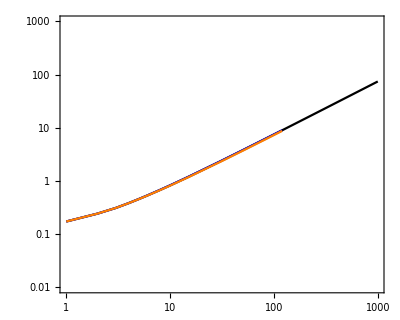

```mathematica
Show[
ListLogLogPlot[
{resList, resList1, resList2},
PlotRange->{{1, 1000},{0.01, 1000}}, Joined->True,
PlotStyle->{Black, Blue, Orange}
(*PlotMarkers->{Automatic, Medium}*)
],
Frame->True,
AspectRatio->0.8,
FrameStyle->Directive[14]
(*FrameLabel->{"Cluster size", "Fisher info"}*)
]
```

```mathematica
fig0=-Graphics-
```

-Graphics-

```mathematica
{circle,uptriangle,diamond,square,downtriangle}=Charting`CommonDump`GraphicsOpenPlotMarkers[][[;;5]];
```

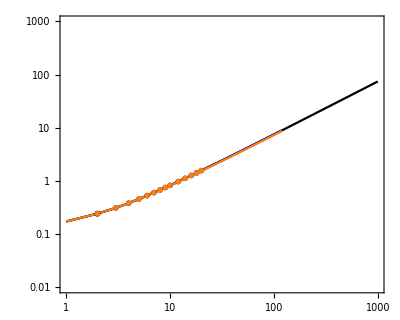

```mathematica
Show[
fig0,
ListLogLogPlot[
{{{2,  0.24401320}},
{
{2, 0.24401320},
{3, 0.31191444},
{4, 0.384844},
{5, 0.4587261},
{6, 0.53224},
{7, 0.606023},
{ 8, 0.679822},
{9, 0.7536558},
{10, 0.82752},
{12, 0.975317},
{14, 1.1231657823976797},
{16, 1.271916529809787},
{18, 1.41991662864993},
{20, 1.567930379725189}
},
{
{2, 0.24401320450189415},
{3,0.3119143050037037},
{4,0.3848376352448799121`9.},
{5,0.4584031980967759},
{6,0.5322093394519466},
{7,0.6059783210169942},
{8,0.679762446382953},
{9,0.7535800122676626},
{10,0.827429061344869},
{12,0.9751926508927057},
{14,1.1230075323283877},
{16,1.2717242771995008},
{18,1.4196902952834343},
{20,1.5676698050242006}
}
}, PlotMarkers->{circle}, PlotStyle->{Black, Blue, Orange}
]
]
```